## Brian — PS 15 — 2025-04-01 — Solution

## EIWL3 Sections 37 and 38

## !! 38.5 and 38.6 were surprising !!

## Exercises from EIWL3 Section 37

```mathematica
(* 37.1 *) Array[Framed[#,Background->If[EvenQ[#],Yellow,LightGray]]&,100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
(* 37.2 *)  Array[If[PrimeQ[#],Framed[#],#]&,100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
(* 37.3 *) Array[If[PrimeQ[#],Labeled[Framed[#,Background->LightGray],Mod[#,4]],#]&,100]
```

{1,22,33,4,51,6,73,8,9,10,113,12,131,14,15,16,171,18,193,20,21,22,233,24,25,26,27,28,291,30,313,32,33,34,35,36,371,38,39,40,411,42,433,44,45,46,473,48,49,50,51,52,531,54,55,56,57,58,593,60,611,62,63,64,65,66,673,68,69,70,713,72,731,74,75,76,77,78,793,80,81,82,833,84,85,86,87,88,891,90,91,92,93,94,95,96,971,98,99,100}

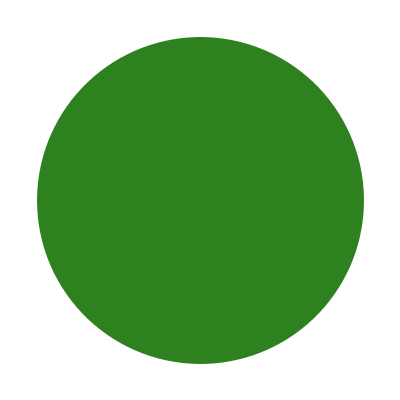

```mathematica
Graphics[{RandomColor[],Disk[]}]
```

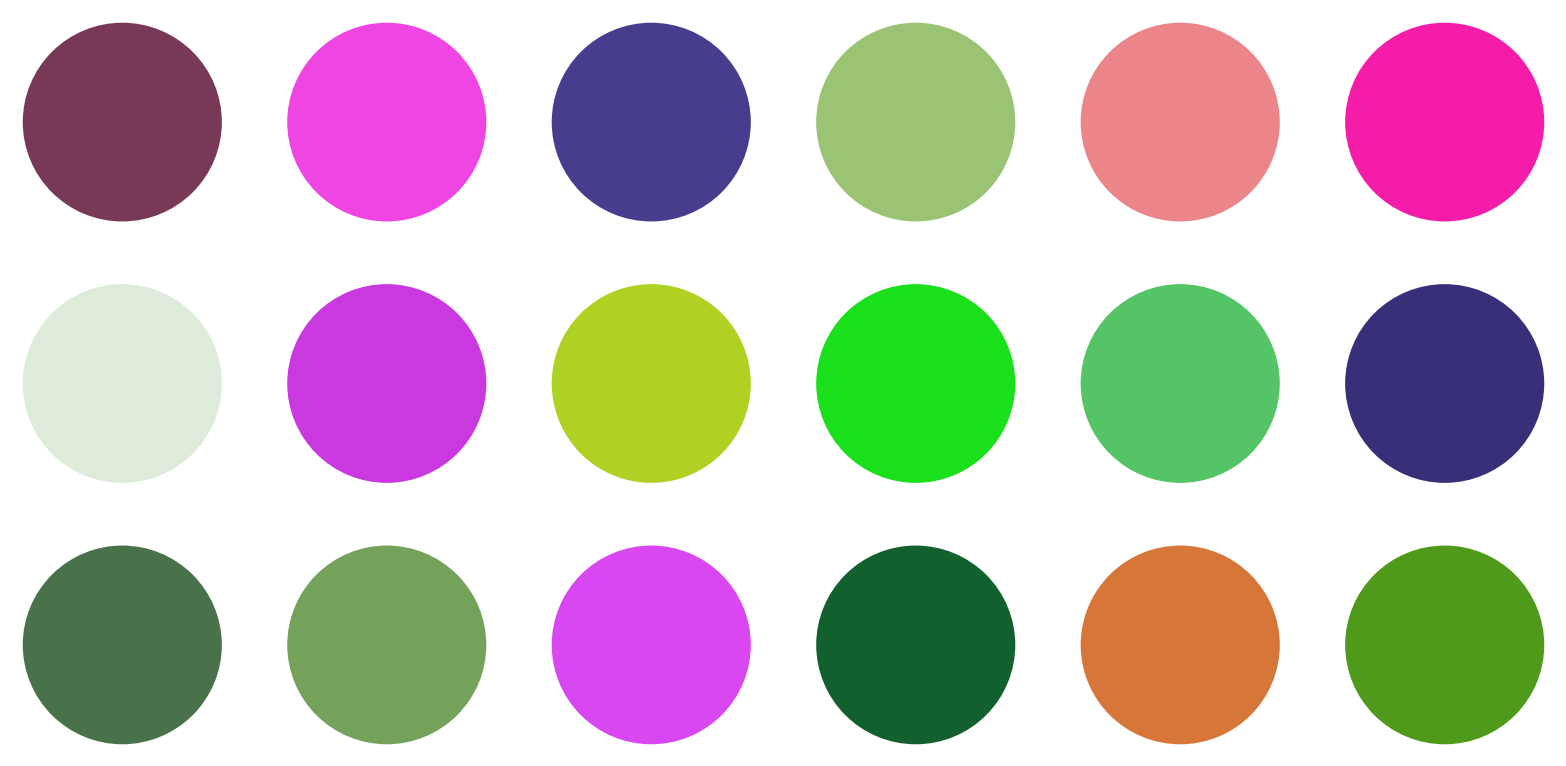

```mathematica
(* 37.4 *) GraphicsGrid[Table[Graphics[{RandomColor[],Disk[]}],3,6]]
```

```mathematica
(* 37.5 *) countries=EntityList[EntityClass["Country","GroupOf5"]];
PieChart[Labeled[#["GDP"],#]&/@countries]
```

-Graphics-

```mathematica
(* 37.6 *) 
PieChart[Labeled[#["Population"],#]&/@countries]
```

-Graphics-

```mathematica
(* 37.7 *) pieCharts = PieChart[Counts[#]]&/@Array[IntegerDigits[2^#]&,25];
GraphicsGrid[Partition[pieCharts,5]]
```

-Graphics-

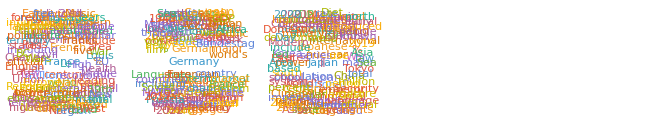

```mathematica
(* 37.8 *)
countryNames = EntityValue[countries,"Name"];
wordClouds = WordCloud[WikipediaData[#]]&/@countryNames;
GraphicsRow[wordClouds]
```

## Exercises from EIWL3 Section 38

```mathematica
(* 38.1 *) Module[{x=Range[10]},x^2+x]
```

{2,6,12,20,30,42,56,72,90,110}

```mathematica
(* 38.2 *) Module[{x=RandomInteger[100,10]},Column[{x,Sort[x],Max[x],Total[x]}]]
```

{43,55,42,38,40,64,88,9,49,50}
{9,38,40,42,43,49,50,55,64,88}
88
478

```mathematica
(* 38.3 *) Module[{pic=Entity["TaxonomicSpecies","GiraffaCamelopardalis::y5488"][EntityProperty["TaxonomicSpecies","Image"]]},ImageCollage[{pic,Blur[pic],EdgeDetect[pic],ColorNegate[pic]}]]
```

-Graphics-

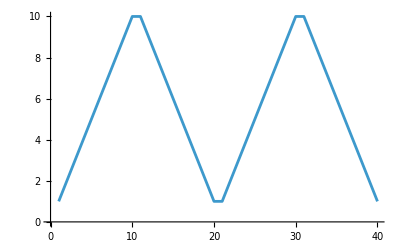

```mathematica
(* 38.4 *) Module[{r=Range[10]},ListLinePlot[Join[r,Reverse[r],r,Reverse[r]]]]
```

```mathematica
(* 38.5 *) (* First, here is what we are being asked to make (but more simply): *)
{Range[10]+1,Range[10]-1,Reverse[Range[10]]}
```

{{2,3,4,5,6,7,8,9,10,11},{0,1,2,3,4,5,6,7,8,9},{10,9,8,7,6,5,4,3,2,1}}

```mathematica
(* We could make that like this: *)
Module[{x=Range[10]},{x+1,x-1,11-x}]
```

{{2,3,4,5,6,7,8,9,10,11},{0,1,2,3,4,5,6,7,8,9},{10,9,8,7,6,5,4,3,2,1}}

```mathematica
(* Wow did that teach me something. I thought the above was *)
(* going to give: *)
(* {{2, 0, 10},{3,1,9}, ..., {11,9,1}} *)
(* and that then I was then going to have to do a Transpose. Module is weird! *)
```

```mathematica
(* 38.6 *) (* First, here is what we are being asked to make (but more simply): *)Module[{u=10},Join[{u},Table[u=Mod[17u+2,11],20]]]
```

{10,7,0,2,3,9,1,8,6,5,10,7,0,2,3,9,1,8,6,5,10}

```mathematica
(* Well, that is easy with NestList: *)
NestList[Mod[17#+2,11]&,10,20]
```

{10,7,0,2,3,9,1,8,6,5,10,7,0,2,3,9,1,8,6,5,10}

```mathematica
(* 38.7 *) (* Probably not what Wolfram had in mind, but it works: *)StringJoin/@Table[If[OddQ[j],RandomChoice[Complement[Alphabet[],{"a","e","i","o","u"}]],
RandomChoice[{"a","e","i","o","u"}]],{i,10},{j,5}]
```

{tejik,bedik,hojuj,likim,yanac,cemav,notaf,zaris,hegan,bohiz}